```mathematica
q= Import["C:\Users\HazemF\Desktop\2.dat"];
```

```mathematica
ListPlot[q];
```

```mathematica
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null] (*Delete duplicate*);
```

```mathematica
ListPlot[q1];
```

```mathematica
q2 = Map[({First[#]-0.2945,Last[#]})&,q1]; (*Shifting X-axis*)
```

```mathematica
q3 = Interpolation[q2]
```

InterpolatingFunction[{{0., 69.9193}}, <>]

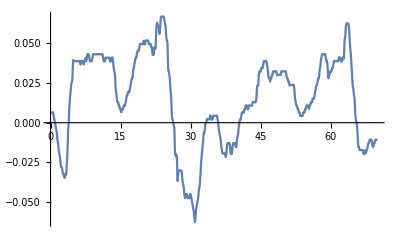

```mathematica
Plot[q3[t],{t,0,70}(*,PlotRange-> {{0,110},{-0.03,0.03}}*)]
```